```mathematica
Length[deps2]
```

100

```mathematica
deps3bis=ReadList["d:\\grofs\\dependencies-more3.txt",Expression,500000]
```

{{2,5,{3,3<->4,3<->5}},{2,5,{3,1<->5,3<->5}},{2,5,{3,2<->5,2<->4}},{2,5,{3,2<->5,4<->5}},{2,5,{3,2<->5,1<->5}},{2,5,{3,4<->5,3<->5}},{2,5,{3,1<->5,2<->5}},{2,5,{3,3<->5,3<->4}},{2,5,{3,3<->5,4<->5}},{2,5,{3,3<->5,1<->5}},{2,5,{3,4<->5,2<->5}},499978,{5891,48261,{3,2<->7,1<->7}},{5891,48261,{3,2<->12,2<->5}},{5891,48261,{3,7<->12,5<->7}},{5891,48261,{3,5<->12,2<->5}},{5891,48261,{3,7<->12,2<->7}},{5891,48261,{3,5<->7,3<->7}},{5891,48261,{3,5<->7,3<->5}},{5892,48267,{3,2<->5,5<->7}},{5892,48267,{3,2<->6,2<->9}},{5892,48267,{3,2<->6,6<->9}},{5892,48267,{3,5<->6,5<->10}}}
 |  |  |  |

```mathematica
deps2bis=ReadList["d:\\grofs\\dependencies-more2.txt",Expression,100000]
```

{{1,3,{2,3<->4,1<->2}},{2,4,{2,1<->5,2<->3}},{2,4,{2,2<->5,1<->4}},{2,5,{2,3<->5,1<->4}},{3,8,{2,4<->5,3<->6}},{3,8,{2,2<->6,3<->5}},{3,9,{2,4<->6,3<->5}},{3,9,{2,5<->6,2<->4}},{4,10,{2,3<->4,2<->5}},{4,10,{2,1<->5,3<->6}},{4,10,{2,3<->5,1<->4}},99978,{4363,40071,{2,5<->10,7<->8}},{4363,40071,{2,8<->10,3<->5}},{4363,40071,{2,5<->11,6<->7}},{4363,40071,{2,6<->11,5<->9}},{4363,40071,{2,9<->11,6<->12}},{4363,40071,{2,2<->11,7<->12}},{4363,40071,{2,7<->11,2<->5}},{4363,40071,{2,2<->12,9<->11}},{4363,40071,{2,9<->12,2<->11}},{4363,40071,{2,11<->12,2<->9}},{4364,40073,{2,4<->6,5<->8}}}
 |  |  |  |

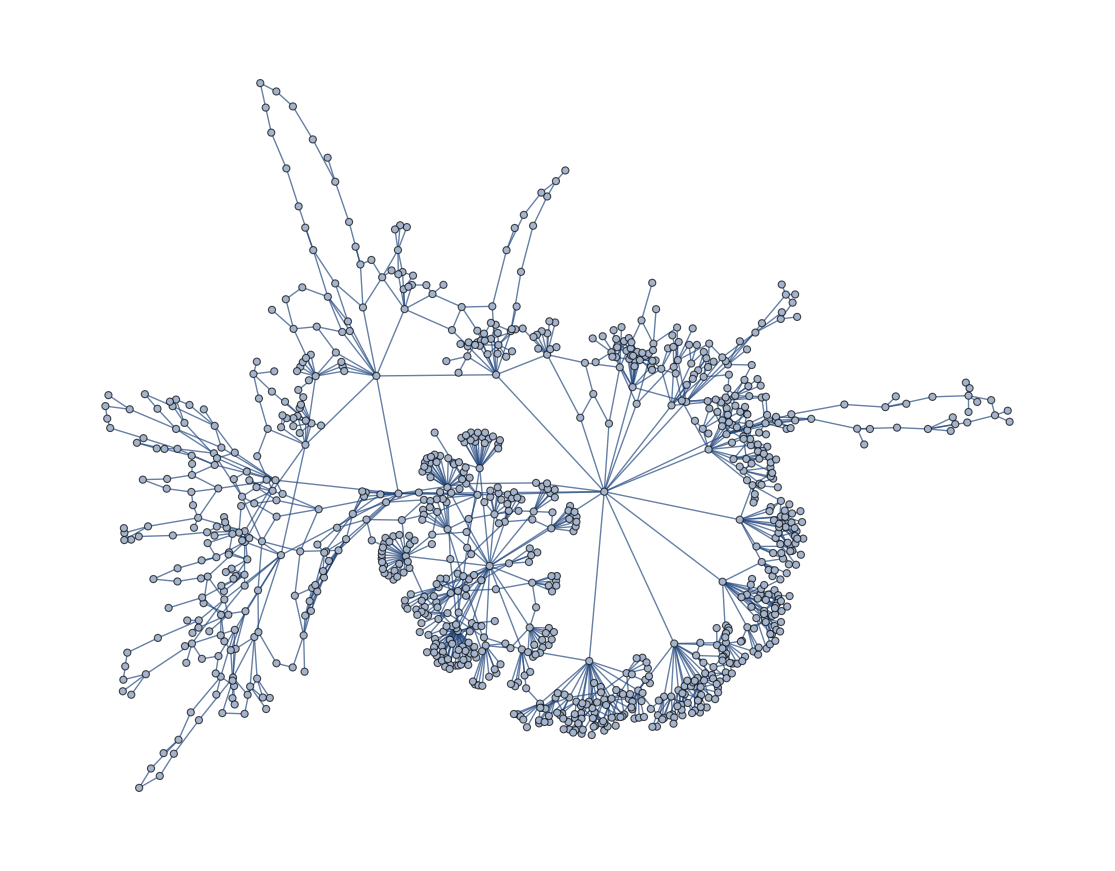

```mathematica
gg=Graph[Sort[DeleteDuplicates[Map[#[[1]]->#[[2]]&,Select[Join[deps2,deps1,deps3, deps2bis, deps3bis],#[[2]]<1556&]]]], DirectedEdges->False]
```

```mathematica
VertexCount[gg]
```

5766

```mathematica
Max[VertexOutDegree[gg]]
```

31

```mathematica
Sort[Tally[VertexOutDegree[gg]]]
```

{{1,506},{2,218},{3,79},{4,55},{5,41},{6,21},{7,17},{8,16},{9,7},{10,5},{11,3},{12,5},{13,4},{14,4},{15,2},{16,1},{17,1},{18,1},{19,1},{23,2},{24,1},{31,1}}

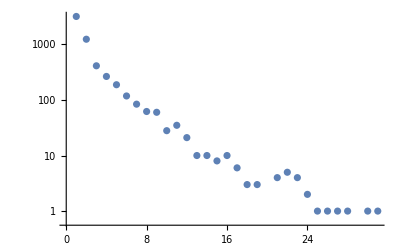

```mathematica
ListLogPlot[Tally[VertexOutDegree[gg]]]
```

```mathematica
Chrom[74]/24
```

1

```mathematica
Table[Chrom[k]/24,{k,Map[#[[2]]&,Select[EdgeList[gg,77<->_],#[[1]]==77&]]}]
```

{4,4,1,1,4,4,1,4,1,3,5,5,1,5,9,4,5,5}

```mathematica
Map[Graph[ReadGrof[#[[2]]],GraphLayout->"PlanarEmbedding"]&,Select[EdgeList[gg,74<->_],#[[1]]==74&]]
```

```mathematica
Select[VertexList[gg],VertexOutDegree[gg,#]==19&]
```

{77}

```mathematica
Chrom[77]/24
```

1

```mathematica
Table[Chrom[k]/24,{k,Map[#[[2]]&,Select[EdgeList[gg,312<->_],#[[1]]==312&]]}]
```

{3,3,4,4,4,16,3,4,5,3,5,5,4,20,20,4,7,5,2,3,6,3,4,4}

```mathematica
Select[VertexList[gg],VertexOutDegree[gg,#]==30&]
```

{307}

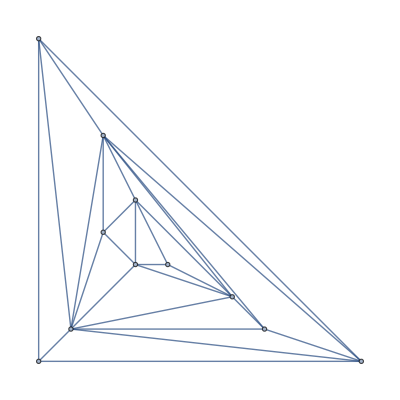

```mathematica
HighlightGraph[Graph[ReadGrof[312],GraphLayout->"PlanarEmbedding"],ReadGraphDiamondHighLights[312]]
```

```mathematica
Table[Chrom[k]/24,{k,Map[#[[2]]&,Select[EdgeList[gg,307<->_],#[[1]]==307&]]}]
```

{4,4,1,12,1,4,4,5,1,1,1,4,5,1,4,4,1,5,1,5,9,1,5,3,5,3,4,5}

```mathematica
Chrom[307]
```

24

```mathematica
Select[VertexList[gg],VertexOutDegree[gg,#]==31&]
```

{74}

```mathematica
EdgeCount[ReadGrof[74]]
```

24

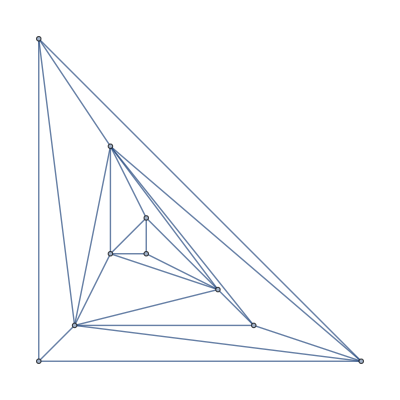

```mathematica
Graph[ReadGrof[74],GraphLayout->"PlanarEmbedding"]
```

```mathematica
Max[Table[{VertexOutDegree[gg,v],v},{v,VertexList[gg]}]]
```

9150

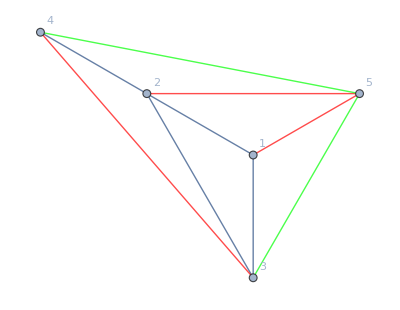

```mathematica
HighlightGraph[Graph[ReadGrof[2],VertexLabels->"Name",GraphLayout->"RadialDrawing"],{Style[{3<->4,1<->5,2<->5},Red],Style[{3<->5,4<->5},Green]}]
```

```mathematica
Table[{k,VertexCount[ReadGrof[k]]},{k,1554-10,1554+10}]
```

{{1544,11},{1545,11},{1546,11},{1547,11},{1548,11},{1549,11},{1550,11},{1551,11},{1552,11},{1553,11},{1554,11},{1555,11},{1556,12},{1557,12},{1558,12},{1559,12},{1560,12},{1561,12},{1562,12},{1563,12},{1564,12}}

```mathematica
{{312,1758,"{3,2<->7,2<->5}"},
{312,1759,"{3,2<->7,1<->7}"},
{312,1759,"{3,2<->5,2<->9}"},
{312,1759,"{3,2<->5,5<->9}"},
{312,1760,"{3,5<->7,3<->5}"},
{312,1760,"{3,1<->7,2<->7}"},
{312,1760,"{3,3<->7,5<->7}"},
{312,1760,"{3,3<->7,3<->5}"},
{312,1760,"{3,3<->7,1<->7}"},
{312,1760,"{3,5<->7,2<->7}"},
{312,1760,"{3,5<->7,2<->5}"},
{312,1761,"{3,3<->5,5<->11}"},
{312,1762,"{3,3<->6,6<->9}"},
{312,1762,"{3,3<->8,3<->11}"},
{312,1762,"{3,3<->8,8<->11}"},
{312,1762,"{3,6<->8,4<->6}"},
{312,1763,"{3,6<->8,3<->6}"},
{312,1764,"{3,4<->6,6<->10}"},
{312,1764,"{3,4<->8,8<->10}"},
{312,1764,"{3,2<->9,2<->5}"},
{312,1764,"{3,2<->9,5<->9}"},
{312,1764,"{3,3<->9,3<->6}"},
{312,1764,"{3,3<->9,6<->9}"},
{312,1764,"{3,3<->9,2<->9}"},
{312,1764,"{3,3<->6,3<->8}"},
{312,1765,"{3,6<->9,5<->9}"},
{312,1765,"{3,6<->9,5<->6}"},
{312,1765,"{3,2<->9,3<->9}"},
{312,1765,"{3,2<->5,2<->7}"},
{312,1765,"{3,2<->5,5<->7}"},
{312,1765,"{3,5<->9,6<->9}"},
{312,1765,"{3,5<->9,5<->6}"},
{312,1766,"{3,5<->9,2<->5}"},
{312,1766,"{3,6<->9,3<->9}"},
{312,1766,"{3,6<->9,3<->6}"},
{312,1766,"{3,5<->6,6<->10}"},
{312,1766,"{3,5<->6,5<->10}"},
{312,1767,"{3,4<->10,8<->10}"},
{312,1767,"{3,6<->10,5<->6}"},
{312,1767,"{3,6<->10,5<->10}"},
{312,1767,"{3,6<->10,4<->6}"},
{312,1767,"{3,6<->10,4<->10}"},
{312,1767,"{3,5<->6,5<->9}"},
{312,1767,"{3,5<->6,6<->9}"},
{312,1767,"{3,5<->10,5<->11}"},
{312,1768,"{3,4<->8,6<->8}"},
{312,1768,"{3,4<->10,6<->10}"},
{312,1768,"{3,8<->10,8<->11}"},
{312,1768,"{3,8<->10,10<->11}"},
{312,1768,"{3,3<->5,3<->7}"},
{312,1768,"{3,3<->5,5<->7}"},
{312,1768,"{3,3<->11,3<->8}"},
{312,1768,"{3,3<->11,8<->11}"},
{312,1768,"{3,5<->11,5<->10}"},
{312,1768,"{3,5<->11,10<->11}"},
{312,1768,"{3,3<->11,3<->5}"},
{312,1768,"{3,3<->11,5<->11}"},
{312,1768,"{3,3<->8,3<->6}"},
{312,1768,"{3,3<->8,6<->8}"},
{312,1768,"{3,8<->11,8<->10}"}
{312,1768,"{3,8<->11,10<->11}"}
{312,1768,"{3,5<->11,3<->5}"}
{312,1768,"{3,5<->11,3<->11}"}
{312,1768,"{3,5<->10,6<->10}"}
{312,1768,"{3,5<->10,5<->6}"}
{312,1768,"{3,10<->11,8<->11}"}
{312,1768,"{3,10<->11,8<->10}"}
{312,1768,"{3,8<->11,3<->11}"}
{312,1768,"{3,8<->11,3<->8}"}
{312,1768,"{3,8<->10,4<->8}"}
{312,1768,"{3,8<->10,4<->10}"}
{312,1768,"{3,10<->11,5<->11}"}
{312,1768,"{3,10<->11,5<->10}"}
```

```mathematica
{312,1733,"{2,1<->7,2<->3}"}
{312,1734,"{2,3<->8,6<->11}"}
{312,1735,"{2,4<->6,8<->10}"}
{312,1736,"{2,4<->8,6<->10}"}
{312,1737,"{2,2<->9,3<->5}"}
{312,1738,"{2,3<->9,2<->6}"}
{312,1739,"{2,6<->9,3<->5}"}
{312,1740,"{2,4<->10,6<->8}"}
{312,1741,"{2,6<->10,4<->5}"}
{312,1742,"{2,8<->10,4<->11}"}
{312,1743,"{2,3<->11,5<->8}"}
{312,1744,"{2,5<->11,3<->10}"}
{312,1745,"{2,8<->11,3<->10}"}
```

```mathematica
r2={{312,1733,"{2,2<->7,1<->5}"},
{312,1733,"{2,2<->5,7<->9}"},
{312,1733,"{2,5<->7,2<->3}"},
{312,1733,"{2,3<->7,1<->5}"},
{312,1733,"{2,3<->5,7<->11}"},
{312,1733,"{2,3<->6,8<->9}"},
{312,1734,"{2,6<->8,3<->4}"},
{312,1739,"{2,5<->9,2<->6}"},
{312,1739,"{2,5<->6,9<->10}"},
{312,1741,"{2,5<->10,6<->11}"},
{312,1745,"{2,10<->11,5<->8}"},
{312,1733,"{2,1<->7,2<->3}"},
{312,1734,"{2,3<->8,6<->11}"},
{312,1735,"{2,4<->6,8<->10}"},
{312,1736,"{2,4<->8,6<->10}"},
{312,1737,"{2,2<->9,3<->5}"},
{312,1738,"{2,3<->9,2<->6}"},
{312,1739,"{2,6<->9,3<->5}"},
{312,1740,"{2,4<->10,6<->8}"},
{312,1741,"{2,6<->10,4<->5}"},
{312,1742,"{2,8<->10,4<->11}"},
{312,1743,"{2,3<->11,5<->8}"},
{312,1744,"{2,5<->11,3<->10}"},
{312,1745,"{2,8<->11,3<->10}"},
}
```

{{312,1733,{2,2<->7,1<->5}},{312,1733,{2,2<->5,7<->9}},{312,1733,{2,5<->7,2<->3}},{312,1733,{2,3<->7,1<->5}},{312,1733,{2,3<->5,7<->11}},{312,1733,{2,3<->6,8<->9}},{312,1734,{2,6<->8,3<->4}},{312,1739,{2,5<->9,2<->6}},{312,1739,{2,5<->6,9<->10}},{312,1741,{2,5<->10,6<->11}},{312,1745,{2,10<->11,5<->8}},{312,1733,{2,1<->7,2<->3}},{312,1734,{2,3<->8,6<->11}},{312,1735,{2,4<->6,8<->10}},{312,1736,{2,4<->8,6<->10}},{312,1737,{2,2<->9,3<->5}},{312,1738,{2,3<->9,2<->6}},{312,1739,{2,6<->9,3<->5}},{312,1740,{2,4<->10,6<->8}},{312,1741,{2,6<->10,4<->5}},{312,1742,{2,8<->10,4<->11}},{312,1743,{2,3<->11,5<->8}},{312,1744,{2,5<->11,3<->10}},{312,1745,{2,8<->11,3<->10}},Null}

```mathematica
Transf[list_]:=Block[
{l, result, chunk, colors ={Red,Yellow,Black,Blue,Purple,Green,Orange, Darker[Green], Darker[Blue], Darker[Red]}, i},
result={};
(*result=Table[Style[Read[Rest[StringToStream[list[[i,3]]]]],Thick,colors[[i]]],{i,1,Length[list]}];*)
result=Table[Style[Rest[Read[StringToStream[list[[i,3]]]]],If[Chrom[list[[i,2]]]/24<4,Dashed,Automatic],Thick,colors[[Mod[list[[i,2]],Length[colors]]+1]]],{i,1,Length[list]}];
Return[result]
]
```

```mathematica
Title[list_]:=Block[
{l, result, chunk, colors ={Red,Yellow,Black,Blue,Purple,Green,Orange, Darker[Green], Darker[Blue], Darker[Red]}, i},
result={};
(*result=Table[Style[Read[Rest[StringToStream[list[[i,3]]]]],Thick,colors[[i]]],{i,1,Length[list]}];*)
result=DeleteDuplicates[Table[Style[{list[[i,2]]->Chrom[list[[i,2]]]/24},colors[[Mod[list[[i,2]],Length[colors]]+1]]],{i,1,Length[list]}]];
Return[result]
]
```

```mathematica
ColorData[109,"ColorList"]
```

{RGBColor[1., 0.4, 0.],RGBColor[0.655728, 0.8, 0.],RGBColor[0., 0.742291, 0.873126],RGBColor[1., 0.656408, 0.],RGBColor[0.893126, 0.4, 0.767184],RGBColor[0.295048, 0.8, 0.286932],RGBColor[0.238758, 0.610466, 1.],RGBColor[1., 0.325204, 0.406504],RGBColor[0., 0.786874, 0.739379],RGBColor[1., 0.520437, 0.],RGBColor[0.7529330319872088, 0.4176501130047967, 1.],RGBColor[0.5572809000084149, 0.8, 0],RGBColor[1., 0.06811595600706821, 0.0851449450088353],RGBColor[0, 0.7226017980018511, 0.9321946059944466],RGBColor[1., 0.7154761789941944, 0]}

```mathematica
InputForm[Title[{{312,1733,"{2,2<->7,1<->5}"},{312,1733,"{2,2<->5,7<->9}"},{312,1733,"{2,5<->7,2<->3}"},{312,1733,"{2,3<->7,1<->5}"},{312,1733,"{2,3<->5,7<->11}"},{312,1733,"{2,3<->6,8<->9}"},{312,1734,"{2,6<->8,3<->4}"},{312,1739,"{2,5<->9,2<->6}"},{312,1739,"{2,5<->6,9<->10}"},{312,1741,"{2,5<->10,6<->11}"},{312,1745,"{2,10<->11,5<->8}"}}]]
```

{Style[{1733 -> 3}, RGBColor[0, 0, 1]], Style[{1733 -> 3}, RGBColor[0, 0, 1]], Style[{1733 -> 3}, RGBColor[0, 0, 1]], Style[{1733 -> 3}, RGBColor[0, 0, 1]], 
 Style[{1733 -> 3}, RGBColor[0, 0, 1]], Style[{1733 -> 3}, RGBColor[0, 0, 1]], Style[{1734 -> 3}, RGBColor[0.5, 0, 0.5]], Style[{1739 -> 3}, RGBColor[2/3, 0, 0]], 
 Style[{1739 -> 3}, RGBColor[2/3, 0, 0]], Style[{1741 -> 5}, GrayLevel[0]], Style[{1745 -> 4}, RGBColor[0, 1, 0]]}

```mathematica
values={{312,1733,"{2,2<->7,1<->5}"},{312,1733,"{2,2<->5,7<->9}"},{312,1733,"{2,5<->7,2<->3}"},{312,1733,"{2,3<->7,1<->5}"},{312,1733,"{2,3<->5,7<->11}"},{312,1733,"{2,3<->6,8<->9}"},{312,1734,"{2,6<->8,3<->4}"},{312,1739,"{2,5<->9,2<->6}"},{312,1739,"{2,5<->6,9<->10}"},{312,1741,"{2,5<->10,6<->11}"},{312,1745,"{2,10<->11,5<->8}"},{312,1733,"{2,1<->7,2<->3}"},{312,1734,"{2,3<->8,6<->11}"},{312,1735,"{2,4<->6,8<->10}"},{312,1736,"{2,4<->8,6<->10}"},{312,1737,"{2,2<->9,3<->5}"},{312,1738,"{2,3<->9,2<->6}"},{312,1739,"{2,6<->9,3<->5}"},{312,1740,"{2,4<->10,6<->8}"},{312,1741,"{2,6<->10,4<->5}"},{312,1742,"{2,8<->10,4<->11}"},{312,1743,"{2,3<->11,5<->8}"},{312,1744,"{2,5<->11,3<->10}"},{312,1745,"{2,8<->11,3<->10}"}}
```

{{312,1733,{2,2<->7,1<->5}},{312,1733,{2,2<->5,7<->9}},{312,1733,{2,5<->7,2<->3}},{312,1733,{2,3<->7,1<->5}},{312,1733,{2,3<->5,7<->11}},{312,1733,{2,3<->6,8<->9}},{312,1734,{2,6<->8,3<->4}},{312,1739,{2,5<->9,2<->6}},{312,1739,{2,5<->6,9<->10}},{312,1741,{2,5<->10,6<->11}},{312,1745,{2,10<->11,5<->8}},{312,1733,{2,1<->7,2<->3}},{312,1734,{2,3<->8,6<->11}},{312,1735,{2,4<->6,8<->10}},{312,1736,{2,4<->8,6<->10}},{312,1737,{2,2<->9,3<->5}},{312,1738,{2,3<->9,2<->6}},{312,1739,{2,6<->9,3<->5}},{312,1740,{2,4<->10,6<->8}},{312,1741,{2,6<->10,4<->5}},{312,1742,{2,8<->10,4<->11}},{312,1743,{2,3<->11,5<->8}},{312,1744,{2,5<->11,3<->10}},{312,1745,{2,8<->11,3<->10}}}

{{383,3044,{2,3<->7,1<->5}},{383,3045,{2,5<->7,3<->11}},{383,3045,{2,3<->8,5<->6}},{383,3047,{2,4<->8,5<->6}},{383,3047,{2,3<->6,8<->9}},{383,3048,{2,4<->6,8<->10}},{383,3048,{2,2<->9,3<->5}},{383,3048,{2,3<->9,2<->6}},{383,3049,{2,2<->5,9<->11}},{383,3051,{2,5<->10,4<->9}},{383,3052,{2,9<->10,5<->6}},{383,3052,{2,1<->11,2<->7}},{383,3052,{2,2<->11,1<->5}},{383,3052,{2,7<->11,1<->5}},{383,3052,{2,5<->11,2<->7}}}

```mathematica
ChromaticPolynomial[ReadGrof[312],4]/24
```

4

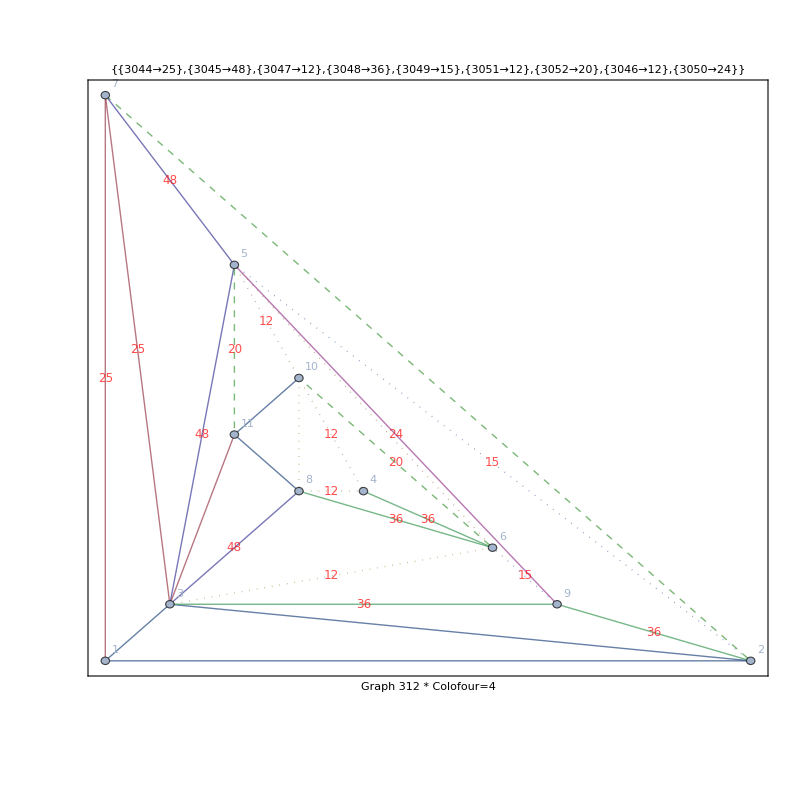

```mathematica
With[
{gn=312, val=values2},
HighlightGraph[Graph[ReadGrof[gn],VertexLabels->"Name",EdgeLabelStyle->Directive[Red,Italic,12],GraphLayout->"PlanarEmbedding",Frame->True,FrameLabel->"Graph "<>ToString[gn]<> " * Colofour=" <> ToString[Chrom[gn]/24], PlotLabel->Title[val],ImageSize->800,EdgeLabels->Edges[val]],Join[
Transf[val],
ReadGraphDiamondHighLights[gn]
]]
]
```

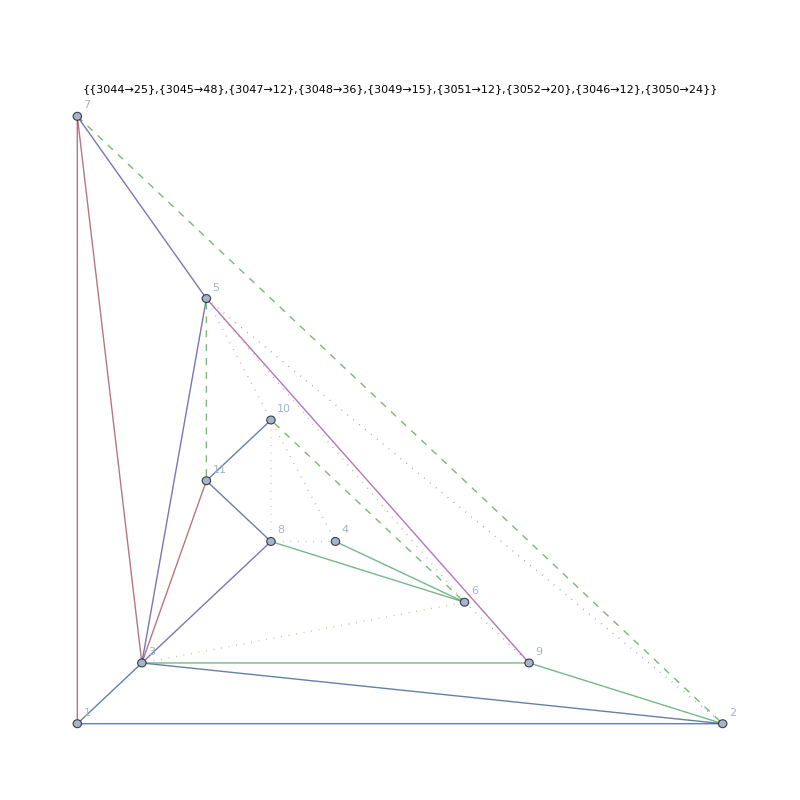

```mathematica
HighlightGraph[Graph[ReadGrof[312],VertexLabels->"Name",GraphLayout->"PlanarEmbedding",PlotLabel->Title[values2],ImageSize->800],Join[
Transf[values2],
ReadGraphDiamondHighLights[312]
]]
```

```mathematica
ChromaticPolynomial[ Rule2[ReadGrof[312],1<->3,2<->7],4]/24
```

4

```mathematica
Map[Chrom[#[[2]]]/24&,{{312,1733,"{2,2<->7,1<->5}"},{312,1733,"{2,2<->5,7<->9}"},{312,1733,"{2,5<->7,2<->3}"},{312,1733,"{2,3<->7,1<->5}"},{312,1733,"{2,3<->5,7<->11}"},{312,1733,"{2,3<->6,8<->9}"},{312,1734,"{2,6<->8,3<->4}"},{312,1739,"{2,5<->9,2<->6}"},{312,1739,"{2,5<->6,9<->10}"},{312,1741,"{2,5<->10,6<->11}"},{312,1745,"{2,10<->11,5<->8}"}}]
```

{3,3,3,3,3,3,3,3,3,5,4}

```mathematica
Chrom[312]/24
```

4

```mathematica
ReadGraphDiamondHighLights[312]
```

{}

```mathematica
DeleteDuplicates[Flatten[Join[FindHamiltonianCycle[ReadGrof[312],80]]]]
```

{1<->2,2<->9,9<->6,6<->4,4<->8,8<->3,3<->11,11<->10,10<->5,5<->7,7<->1,6<->10,10<->4,11<->5,4<->10,10<->8,6<->3,11<->8,8<->4,9<->3,8<->6,6<->5,10<->6,4<->6,8<->10,6<->8,10<->11,11<->3,3<->5,8<->11,5<->11,3<->7,2<->5,5<->9,9<->5,5<->6,5<->10,2<->3,6<->9,1<->7,7<->2,3<->1,7<->5,5<->2,2<->7,3<->8,3<->6}

```mathematica
Sort[Map[Chrom[#]/(24*4)&, Select[Range[2000],EulerianGraphQ[ReadGrof[#]]&]]]
```

{1,3,4,7,10,11,12}